```mathematica
{{data = Import["E:\\Alessio\\Desktop\\Computazionale\\es9\\data.txt","Table"]}, {}};
model = a*x^b
```

a x^b

```mathematica
Cont = Take[data, -60][[All, {1,2, 4 , 6, 8, 10, 12, 14, 16}]];
Disc = Take[data,-60][[All, {1,3, 5 , 7,9, 11, 13, 15, 17}]];
```

```mathematica
GraphicsRow[{ListPlot[{ Take[Disc][[All, {1,2}]],Take[Cont][[All, {1,2}]]},  PlotRange->All],ListLogPlot[{ Take[Disc][[All, {1,3}]],Take[Cont][[All, {1,3}]]}, PlotRange->All],ListPlot[{ Take[Disc][[All, {1,4}]],Take[Cont][[All, {1,4}]]}, PlotLegends->{ "Discontinua","Continua"}, PlotRange->All]},ImageSize->Full]
```

-Graphics-

# Media

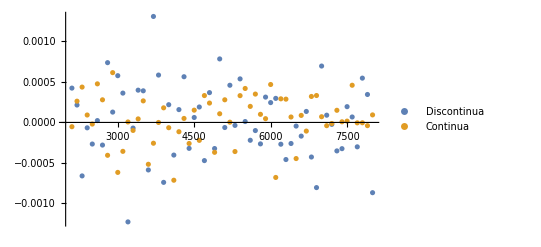

```mathematica
ListPlot[{ Take[Disc][[All, {1,2}]],Take[Cont][[All, {1,2}]]}, PlotLegends->{ "Discontinua","Continua"}, PlotRange->All]
```

# Varianza

```mathematica
linecont=FindFit[Take[Cont][[All, {1,3}]], model,{a,b},x]
linedisc=FindFit[Take[Disc][[All, {1,3}]], model,{a,b},x]
```

{a→0.423206893822651552348400480633181809745266143,b→-1.02820311631945062402428235757204395244686387}

{a→1.027359951366886589503867942499175050566570956,b→-1.002411566070615264880468548921828755915002345}

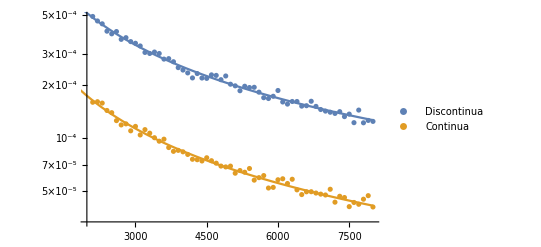

```mathematica
Show[{ListLogPlot[{ Take[Disc][[All, {1,3}]],Take[Cont][[All, {1,3}]]}, PlotLegends->{ "Discontinua","Continua"}, PlotRange->All],LogPlot[{model/.linedisc,model/.linecont},{x,0,8000}]}]
```

# Skeweness

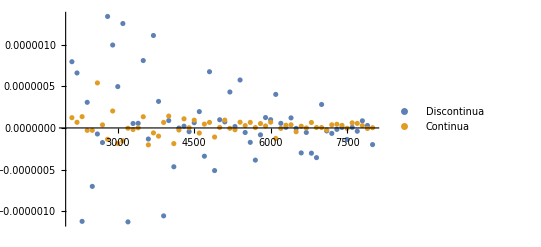

```mathematica
ListPlot[{ Take[Disc][[All, {1,4}]],Take[Cont][[All, {1,4}]]}, PlotLegends->{ "Discontinua","Continua"}, PlotRange->All]
```

# Kurtosis

```mathematica
linecont=FindFit[Take[Cont][[All, {1,5}]], model,{a,b},x]
linedisc=FindFit[Take[Disc][[All, {1,5}]], model,{a,b},x]
```

{a→0.78833144174338814765732517258477035671522,b→-2.1004502091622186511509860151459088906986}

{a→4.91735849997394742494286236709105016833761,b→-2.0609397391980269583571592246237074242889}

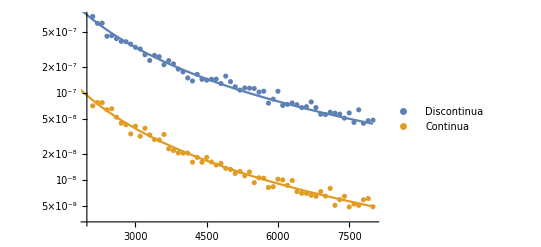

```mathematica
Show[{ListLogPlot[{ Take[Disc][[All, {1,5}]],Take[Cont][[All, {1,5}]]}, PlotLegends->{ "Discontinua","Continua"}, PlotRange->All], LogPlot[{model/.linedisc,model/.linecont},{x,0,8000}]}]
```

# Quinto

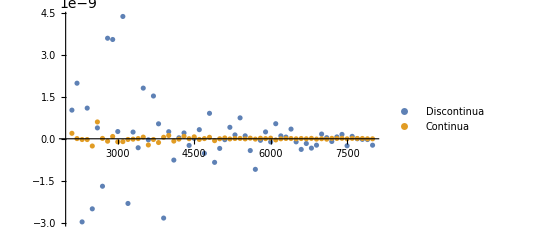

```mathematica
ListPlot[{ Take[Disc][[All, {1,6}]],Take[Cont][[All, {1,6}]]}, PlotLegends->{ "Discontinua","Continua"}, PlotRange->All]
```

# Sesto

```mathematica
linecont=FindFit[Take[Cont][[All, {1,7}]], model,{a,b},x]
linedisc=FindFit[Take[Disc][[All, {1,7}]], model,{a,b},x,MaxIterations->1000]
```

{a→0.3876981179786234334199878152975175017,b→-2.937359205746013733651679435161527981}

{a→538.844510248350631539392534560471447827,b→-3.45465332247874428253645960103995603801}

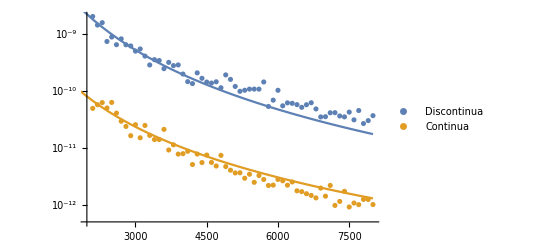

```mathematica
Show[{ListLogPlot[{ Take[Disc][[All, {1,7}]],Take[Cont][[All, {1,7}]]}, PlotLegends->{ "Discontinua","Continua"}, PlotRange->All],LogPlot[{model/.linedisc,model/.linecont},{x,0,8000}]}]
```

# Rapporti

## 4/2

```mathematica
linecont=FindFit[Take[Cont][[All, {1,8}]], model,{a,b},x]
linedisc=FindFit[Take[Disc][[All, {1,8}]], model,{a,b},x]
```

{a→1.949360143474772297707522744993097230327027723,b→-1.078237005309675547581331914562742392619485663}

{a→2.875232449526114917909447080665824620284330146,b→-0.9950956539301232164749362670524705795857766199}

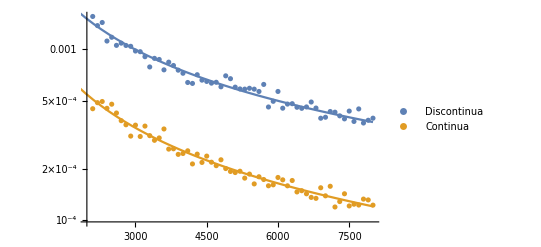

```mathematica
Show[{ListLogPlot[{ Take[Disc][[All, {1,8}]],Take[Cont][[All, {1,8}]]}, PlotLegends->{ "Discontinua","Continua"}, PlotRange->All], LogPlot[{model/.linedisc,model/.linecont},{x,0,8000}]}]
```

## 6/4

```mathematica
linecont=FindFit[Take[Cont][[All, {1,9}]], model,{a,b},x]
linedisc=FindFit[Take[Disc][[All, {1,9}]], model,{a,b},x]
```

{a→3.517240790974178313120854151237656497140291551,b→-1.087442166911353551991246492853218208176580386}

{a→3.946956565307391616660576293334852895274186237,b→-0.9733371178410272822573729735966928040842143412}

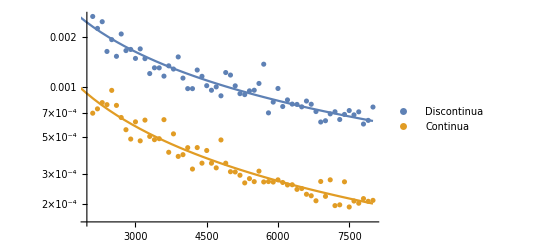

```mathematica
Show[{ListLogPlot[{ Take[Disc][[All, {1,9}]],Take[Cont][[All, {1,9}]]}, PlotLegends->{ "Discontinua","Continua"}, PlotRange->All],LogPlot[{model/.linedisc,model/.linecont},{x,0,8000}]}]
```